### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{7,U1},{8,U2},{9,U3}},Switching Costs→{}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)1(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)0,S2->(*S123*)3,S3->3,S4->3,S5->0,S6->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

{u1,u10,u11,u12,u16,u18,u2,u20,u4}

-j1+j2-u1+u2==cpc1&&-j3+j4-u1+u4==cpc2&&-j5+j6+u11-u2==cpc3&&-j7+j8+u11-u4==cpc4&&j10-j9+u10-u4==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u10+u12==cpc7&&-j15+j16-u10+u16==cpc8&&-j17+j18-u12+u18==cpc9&&-j19+j20-u16+u20==cpc10&&-j23+j24-u18+u20==cpc11

{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}}

{u1,u2,u1,u4,u2,u11,u4,u11,u4,u10,u11,u12,u10,u12,u10,u16,u12,u18,u16,u20,0,0,u18,u20,1,1,u27,u27,u29,u29,u31,u31}

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

```mathematica
bla=Range[7]
```

{1,2,3,4,5,6,7}

```mathematica
0&/@bla
```

{0,0,0,0,0,0,0}

```mathematica
MapThread[Rule,{bla,0&/@bla }]
```

{1→0,2→0,3→0,4→0,5→0,6→0,7→0}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.043891 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j509==0&&jt522==0&&u531==2&&u532==1&&-2≤u533≤1
and the rules are:
<|j512→1,u540→0,u541→1,j507→1,j508→1-j509,j510→1-j509,j511→j509,j513→0,j514→0,j515→0,j516→0,j517→0,j518→0,jt519→0,jt520→1,jt521→1-jt522,jt523→-j509+jt522,jt524→j509-jt522,jt525→j509-jt522,jt526→-j509+jt522,jt527→1-j509,jt528→0,jt529→j509,jt530→0,u534→0,u535→1,u537→-1+u531,u538→-1+j509+u532,u539→-j509+u533,u542→u531,u536→u531|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u533≤1,<|j512→1,u540→0,u541→1,j507→1,j508→1-0,j510→1-0,j511→0,j513→0,j514→0,j515→0,j516→0,j517→0,j518→0,jt519→0,jt520→1,jt521→1-0,jt523→-0+0,jt524→0-0,jt525→0-0,jt526→-0+0,jt527→1-0,jt528→0,jt529→0,jt530→0,u534→0,u535→1,u537→-1+2,u538→-1+0+1,u539→-0+u533,u542→2,u536→2,j509→0,jt522→0,u531→2,u532→1|>}

DataToEquations: There are multiple solutions for the given data.

all ok? up to here?

{j507-j513+IntM[j507-j513,1->2],j508-j514+IntM[j508-j514,2->3],j509-j515+IntM[j509-j515,2->4]}

DataToEquations: Done.

{0.06446,Null}

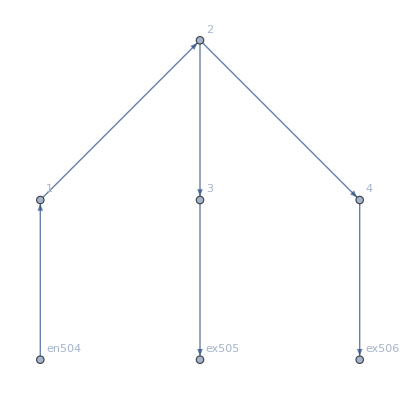

current: <|{1,1->2}→0,{1,en504->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex505}→0,{4,2->4}→0,{4,4->ex506}→0,{en504,en504->1}→0,{ex505,3->ex505}→1,{ex506,4->ex506}→0|>

transition: <|{1,1->2,en504->1}→0,{1,en504->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex505}→1,{3,3->ex505,2->3}→0,{4,2->4,4->ex506}→0,{4,4->ex506,2->4}→0|>

value: <|{1,1->2}→2,{1,en504->1}→2,{2,1->2}→1,{2,2->3}→1,{2,2->4}→u533,{3,2->3}→0,{3,3->ex505}→0,{4,2->4}→u533,{4,4->ex506}→1,{en504,en504->1}→2,{ex505,3->ex505}→0,{ex506,4->ex506}→1|>

```mathematica
(MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)1(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)0,S2->(*S123*)3,S3->3,S4->3,S5->0,S6->0}];)//Timing
If[MFGEquations =!= Null,
Print[MFGEquations["FG"]];
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
]
```

#### In the next example, it looks like we may choose one of the values for the value function. One of the extremes should be the consistent choice.

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)31,S1->1,S2->4,S3->3,S4->5,S5->3,S6->0}];//Timing
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.040963 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j561==0&&jt574==0&&u583==3&&u584==1&&-2≤u585≤1
and the rules are:
<|j564→1,u592→0,u593→31,j559→1,j560→1-j561,j562→1-j561,j563→j561,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1-jt574,jt575→-j561+jt574,jt576→j561-jt574,jt577→j561-jt574,jt578→-j561+jt574,jt579→1-j561,jt580→0,jt581→j561,jt582→0,u586→0,u587→31,u589→-1+u583,u590→-1+j561+u584,u591→-j561+u585,u594→u583,u588→u583|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u585≤1,<|j564→1,u592→0,u593→31,j559→1,j560→1-0,j562→1-0,j563→0,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1-0,jt575→-0+0,jt576→0-0,jt577→0-0,jt578→-0+0,jt579→1-0,jt580→0,jt581→0,jt582→0,u586→0,u587→31,u589→-1+3,u590→-1+0+1,u591→-0+u585,u594→3,u588→3,j561→0,jt574→0,u583→3,u584→1|>}

DataToEquations: There are multiple solutions for the given data.

all ok? up to here?

{j559-j565+IntM[j559-j565,1->2],j560-j566+IntM[j560-j566,2->3],j561-j567+IntM[j561-j567,2->4]}

DataToEquations: Done.

{0.061353,Null}

current: <|{1,1->2}→0,{1,en556->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex557}→0,{4,2->4}→0,{4,4->ex558}→0,{en556,en556->1}→0,{ex557,3->ex557}→1,{ex558,4->ex558}→0|>

transition: <|{1,1->2,en556->1}→0,{1,en556->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex557}→1,{3,3->ex557,2->3}→0,{4,2->4,4->ex558}→0,{4,4->ex558,2->4}→0|>

value: <|{1,1->2}→3,{1,en556->1}→3,{2,1->2}→2,{2,2->3}→1,{2,2->4}→u585,{3,2->3}→0,{3,3->ex557}→0,{4,2->4}→u585,{4,4->ex558}→31,{en556,en556->1}→3,{ex557,3->ex557}→0,{ex558,4->ex558}→31|>

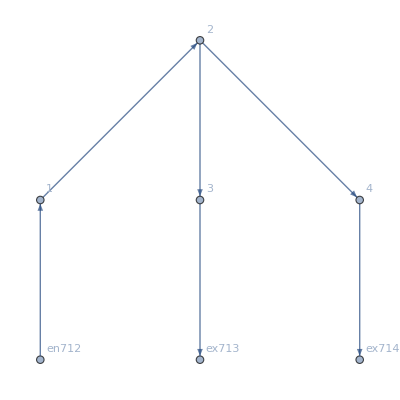

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j507-j513-u531+u537==0.294244&&j508-j514-u532+u538==0.294244&&j509-j515-u533+u539==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j507-j513-u531+u537==0.294244&&j508-j514-u532+u538==0.294244&&j509-j515-u533+u539==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j507→1,j508→1.,j509→0.,j510→1.,j511→0.,j512→1,j513→0,j514→0,j515→0,j516→0,j517→0,j518→0,jt519→0,jt520→1,jt521→1.,jt522→0.,jt523→0,jt524→0,jt525→0,jt526→0,jt527→1.,jt528→0,jt529→0.,jt530→0,u531→1.41151,u532→0.705756,u534→0,u535→1,u536→1.41151,u537→0.705756,u538→0.,u539→0.+1. u533,u540→0,u541→1,u542→1.41151|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==0.27315&&j560-j566-u584+u590==0.27315&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

FRX1: nonlinear: 
j559-j565-u583+u589==0.27315&&j560-j566-u584+u590==0.27315&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→2.4537,u584→0.72685,u586→0,u587→31,u588→2.4537,u589→1.72685,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→2.4537|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==0.226791&&j560-j566-u584+u590==0.226791&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

FRX1: nonlinear: 
j559-j565-u583+u589==0.226791&&j560-j566-u584+u590==0.226791&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→2.54642,u584→0.773209,u586→0,u587→31,u588→2.54642,u589→1.77321,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→2.54642|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==0.0407993&&j560-j566-u584+u590==0.0407993&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j559-j565-u583+u589==0.0407993&&j560-j566-u584+u590==0.0407993&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→2.9184,u584→0.959201,u586→0,u587→31,u588→2.9184,u589→1.9592,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→2.9184|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==0&&j560-j566-u584+u590==0&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57009×10^-15,ComplexInfinity]

<|j559→1,j560→1,j561→0,j562→1,j563→0,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1,jt574→0,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1,jt580→0,jt581→0,jt582→0,u583→3,u584→1,u586→0,u587→31,u588→3,u589→2,u590→0,u591→u585,u592→0,u593→31,u594→3|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.0941008&&j560-j566-u584+u590==-0.0941008&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j559-j565-u583+u589==-0.0941008&&j560-j566-u584+u590==-0.0941008&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→3.1882,u584→1.0941,u586→0,u587→31,u588→3.1882,u589→2.0941,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→3.1882|>

```mathematica
0+0.
```

0.

```mathematica
0+0
```

0

```mathematica
0===
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.278995&&j560-j566-u584+u590==-0.278995&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: nonlinear: 
j559-j565-u583+u589==-0.278995&&j560-j566-u584+u590==-0.278995&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→3.55799,u584→1.27899,u586→0,u587→31,u588→3.55799,u589→2.27899,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→3.55799|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.357381&&j560-j566-u584+u590==-0.357381&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j559-j565-u583+u589==-0.357381&&j560-j566-u584+u590==-0.357381&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→3.71476,u584→1.35738,u586→0,u587→31,u588→3.71476,u589→2.35738,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→3.71476|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.552467&&j560-j566-u584+u590==-0.552467&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j559-j565-u583+u589==-0.552467&&j560-j566-u584+u590==-0.552467&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→4.10493,u584→1.55247,u586→0,u587→31,u588→4.10493,u589→2.55247,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→4.10493|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.676702&&j560-j566-u584+u590==-0.676702&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: nonlinear: 
j559-j565-u583+u589==-0.676702&&j560-j566-u584+u590==-0.676702&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→4.3534,u584→1.6767,u586→0,u587→31,u588→4.3534,u589→2.6767,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→4.3534|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j559-j565-u583+u589==-0.826677&&j560-j566-u584+u590==-0.826677&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

FRX1: nonlinear: 
j559-j565-u583+u589==-0.826677&&j560-j566-u584+u590==-0.826677&&j561-j567-u585+u591==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

<|j559→1,j560→1.,j561→0.,j562→1.,j563→0.,j564→1,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→1,jt573→1.,jt574→0.,jt575→0,jt576→0,jt577→0,jt578→0,jt579→1.,jt580→0,jt581→0.,jt582→0,u583→4.65335,u584→1.82668,u586→0,u587→31,u588→4.65335,u589→2.82668,u590→0.,u591→0.+1. u585,u592→0,u593→31,u594→4.65335|>